# Dynamic analysis

-Graphics-

```mathematica
ClearAll["Global`*"]
```

## Position analysis: direct kinematics

```mathematica
Mrotxtrasl[α_,pt_]:={{1, 0, 0, pt[[1]]}, {0, Cos@α, -Sin@α, pt[[2]]}, {0, Sin@α, Cos@α, pt[[3]]}, {0, 0, 0, 1}}
```

```mathematica
EE={0,L Cos@θ[t],L Sin@θ[t],1};
```

```mathematica
M01=Mrotxtrasl[θ[t],EE];M01//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[θ[t]] | -Sin[θ[t]] | L Cos[θ[t]]
0 | Sin[θ[t]] | Cos[θ[t]] | L Sin[θ[t]]
0 | 0 | 0 | 1)

```mathematica
M02=M01;
```

```mathematica
W01=(D[M01, t]).Inverse@M01//Simplify;W01//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -θ'[t] | 0
0 | θ'[t] | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W02=W01;
```

```mathematica
Lrotx={{0, 0, 0, 0}, {0, 0, -1, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}};
```

```mathematica
L01=Lrotx;
```

Absolute velocity of point E

```mathematica
W01.EE//MatrixForm
```

(0
-L Sin[θ[t]] θ'[t]
L Cos[θ[t]] θ'[t]
0)

## Dynamic analysis

Pseudo inertia matrix

```mathematica
J11={{0, 0, 0, 0}, {0, (m1 L^2)/3, 0, (-m1 L)/2}, {0, 0, 0, 0}, {0, (-m1 L)/2, 0, m1}};
```

```mathematica
J10=M01.J11.Transpose@M01//Simplify;J10//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/3 L^2 m1 Cos[θ[t]]^2 | 1/6 L^2 m1 Sin[2 θ[t]] | 1/2 L m1 Cos[θ[t]]
0 | 1/6 L^2 m1 Sin[2 θ[t]] | 1/3 L^2 m1 Sin[θ[t]]^2 | 1/2 L m1 Sin[θ[t]]
0 | 1/2 L m1 Cos[θ[t]] | 1/2 L m1 Sin[θ[t]] | m1)

```mathematica
T1=1/2 Tr[W01.J10.Transpose@W01]//Simplify
```

1/6 L^2 m1 θ'[t]^2

```mathematica
J21={{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, m2}};
```

```mathematica
J20=M01.J21.Transpose@M01;J20//MatrixForm
```

(0 | 0 | 0 | 0
0 | L^2 m2 Cos[θ[t]]^2 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L m2 Cos[θ[t]]
0 | L^2 m2 Cos[θ[t]] Sin[θ[t]] | L^2 m2 Sin[θ[t]]^2 | L m2 Sin[θ[t]]
0 | L m2 Cos[θ[t]] | L m2 Sin[θ[t]] | m2)

```mathematica
T2=1/2 Tr[W02.J20.Transpose@W02]//Simplify
```

1/2 L^2 m2 θ'[t]^2

```mathematica
Hg1={{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, -g}, {0, 0, 0, 0}};
```

```mathematica
Ug1=-Tr[Hg1.J10]
```

1/2 g L m1 Sin[θ[t]]

```mathematica
Hg2=Hg1;
```

```mathematica
Ug2=-Tr[Hg2.J20]
```

g L m2 Sin[θ[t]]

-Graphics-

```mathematica
Cx=C1+1/3 L F-F01z L;
```

```mathematica
ϕ11={{0, 0, 0, 0}, {0, 0, -Cx, F01y}, {0, Cx, 0, F01z-F}, {0, -F01y, -(F01z-F), 0}};
```

```mathematica
ϕ01=M01.ϕ11.Transpose@M01//Simplify;ϕ01//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | -C1+(2 F L)/3 | F01y Cos[θ[t]]+(F-F01z) Sin[θ[t]]
0 | C1-(2 F L)/3 | 0 | (-F+F01z) Cos[θ[t]]+F01y Sin[θ[t]]
0 | -F01y Cos[θ[t]]+(-F+F01z) Sin[θ[t]] | (F-F01z) Cos[θ[t]]-F01y Sin[θ[t]] | 0)

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]]
```

```mathematica
Q1=PSS[ϕ01,L01]
```

C1-(2 F L)/3

## Equation of motion

```mathematica
Lagr=T1+T2-Ug1-Ug2//Simplify
```

1/6 L (-3 g (m1+2 m2) Sin[θ[t]]+L (m1+3 m2) θ'[t]^2)

```mathematica
dLdθ=D[Lagr, θ[t]]
```

-1/2 g L (m1+2 m2) Cos[θ[t]]

```mathematica
dLdθdot=D[Lagr, θ'[t]]
```

1/3 L^2 (m1+3 m2) θ'[t]

```mathematica
eq=Expand[D[(D[Lagr, θ'[t]]), t]-D[Lagr, θ[t]]-Q1]==0
```

-C1+(2 F L)/3+1/2 g L m1 Cos[θ[t]]+g L m2 Cos[θ[t]]+1/3 L^2 m1 θ''[t]+L^2 m2 θ''[t]==0

```mathematica
eqmotion=eq/.F->α D[θ[t], t]
```

-C1+1/2 g L (m1+2 m2) Cos[θ[t]]+2/3 L α θ'[t]+1/3 L^2 (m1+3 m2) θ''[t]==0

## Response to a sinusoidal input

Example of a direct dynamic problem : the motor applies a sinusoidal torque with 10 s period, and we want to find the resulting motion of the link .

```mathematica
data={L->0.3,m1->15,m2->8,α->5,g->9.81};
```

```mathematica
motor={C1->10 Sin[(2π)/10 t]};
```

```mathematica
e1=eqmotion/.motor/.data
```

45.6165 Cos[θ[t]]-10 Sin[(π t)/5]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
ds1=NDSolve[{e1,θ[0]==0,θ'[0]==0},θ[t],{t,0,100}][[1]]
```

{θ[t]→InterpolatingFunction[…][t]}

Initially, there' s a free oscillation of the arm

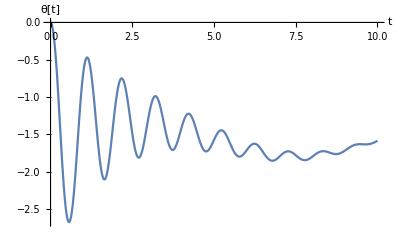

```mathematica
Plot[θ[t]/.ds1,{t,0,10},LabelStyle->Black,AxesLabel->{"t","θ[t]"}]
```

Then it swings at the same frequency of the motor

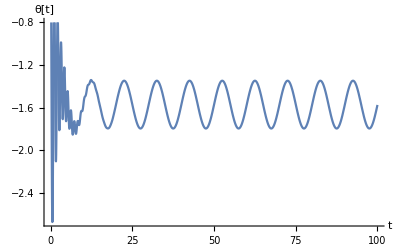

```mathematica
Plot[θ[t]/.ds1,{t,0,100},LabelStyle->Black,AxesLabel->{"t","θ[t]"}]
```

The arm swings downwards about the vertical position (-π/2) initially with high - frequency damped oscillations, then follows the commanded torque (10 s period) . The gravity force needs to be balanced . To do this, we calculate the equilibrium solution of the equation of motion

## Static compensation

Compensation of the gravity

The derivatives must be 0. We want that the arm has to be horizontal

```mathematica
staticeq=eqmotion/.{θ[t]->0,θ'[t]->0,θ''[t]->0}
```

-C1+1/2 g L (m1+2 m2)==0

```mathematica
motor
```

{C1→10 Sin[(π t)/5]}

```mathematica
C1static=Solve[staticeq,C1][[1]]/.data
```

{C1→45.6165}

Now we use this value of C1 into the original equation of motion, which is a differential equation in θ[t] . And we solve numerically setting zero initial conditions :

```mathematica
elstatic=eqmotion/.C1static/.data
```

-45.6165+45.6165 Cos[θ[t]]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dsstatic=NDSolve[{elstatic,θ[0]==0,θ'[0]==0},θ[t],{t,0,100}][[1]]
```

{θ[t]→InterpolatingFunction[…][t]}

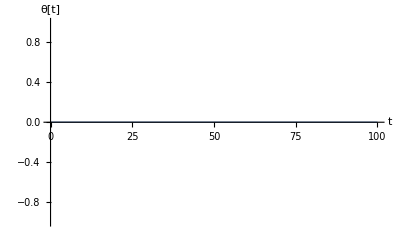

```mathematica
Plot[θ[t]/.dsstatic,{t,0,100},PlotStyle->Thick,LabelStyle->Black,AxesLabel->{"t","θ[t]"}]
```

## Compliance of the actuation chain

-Graphics--Graphics-

We consider here the presence of a compliant transmission belt between the motor and the link . The angular stiffness is K_θ, therefore C1 = K_θ (θm - θ)

Elastic potential energy stored in the belt

```mathematica
Uel=1/2 Subscript[K, θ](θ[t]-θm[t])^2;
```

```mathematica
LagrEl=T1+T2-Ug1-Ug2-Uel//Simplify
```

1/6 (-3 K_θ (θ[t]-θm[t])^2+L (-3 g (m1+2 m2) Sin[θ[t]]+L (m1+3 m2) θ'[t]^2))

Now we don’t have to consider C1 since its contribute is already in Uel

```mathematica
Q1el=PSS[ϕ01,L01]/.C1->0
```

-(2 F L)/3

```mathematica
Q2=C1;
```

```mathematica
eqθ=D[(D[LagrEl, θ'[t]]), t]-D[LagrEl, θ[t]]-Q1el
```

(2 F L)/3+1/6 (3 g L (m1+2 m2) Cos[θ[t]]+6 K_θ (θ[t]-θm[t]))+1/3 L^2 (m1+3 m2) θ''[t]

```mathematica
eqθm=D[(D[LagrEl, θm'[t]]), t]-D[LagrEl, θm[t]]-Q2
```

-C1-K_θ (θ[t]-θm[t])

```mathematica
eqmotθ=eqθ/.F->α D[θ[t], t]
```

1/6 (3 g L (m1+2 m2) Cos[θ[t]]+6 K_θ (θ[t]-θm[t]))+2/3 L α θ'[t]+1/3 L^2 (m1+3 m2) θ''[t]

```mathematica
eqmotθm=eqθm
```

-C1-K_θ (θ[t]-θm[t])

```mathematica
e1el=Simplify[eqmotθ/.data/.motor/.Subscript[K, θ]->10]==0
```

45.6165 Cos[θ[t]]+10. θ[t]-10. θm[t]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
e2el=Simplify[eqmotθm/.data/.motor/.Subscript[K, θ]->10]==0
```

-10 (Sin[(π t)/5]+θ[t]-θm[t])==0

```mathematica
dsel=NDSolve[{e1el,e2el,θ[0]==0,θ'[0]==0,θm[0]==0,θm'[0]==0},{θ[t],θm[t]},{t,0,50}][[1]]
```

{θ[t]→InterpolatingFunction[…][t],θm[t]→InterpolatingFunction[…][t]}

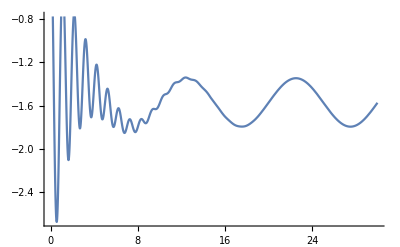

```mathematica
Plot[θ[t]/.dsel,{t,0,30}]
```

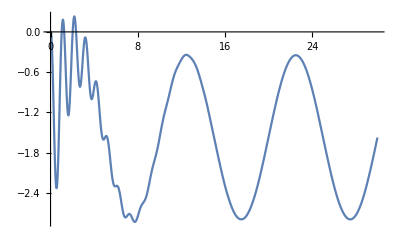

```mathematica
Plot[θm[t]/.dsel,{t,0,30}]
```

## Back to a non - compliant actuation chain : the effect of torque noise

Applying the constant torque the arm is balanced and remains still indefinitely . However, small perturbations are present on the link produced by the external world, which are here modelled as a sinusoidal torque with a small amplitude (0.001 N*m) superimposed to the static torque (45.61 N*m) . 
We see how the system behaves under the combined action of the static torque and the perturbation :

```mathematica
newC1=(C1/.C1static)+0.001 Sin[(2π)/10 t];
```

```mathematica
elbalanced=eqmotion/.C1->newC1/.data
```

-45.6165+45.6165 Cos[θ[t]]-0.001 Sin[(π t)/5]+1. θ'[t]+1.17 θ''[t]==0

```mathematica
dsbalanced=NDSolve[{elbalanced,θ[0]==0,θ'[0]==0},θ[t],{t,0,100}][[1]]
```

{θ[t]→InterpolatingFunction[…][t]}

Unstable behaviour since the maximum gravity torque is when the arm is horizontal and the motor compensates always this. If the arm rotates, the motor exerts more torque than the one of the gravity, then it becomes unstable. A control loop is needed to compute instantaneously the torque needed.

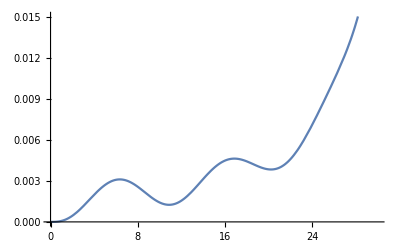

```mathematica
Plot[θ[t]/.dsbalanced,{t,0,30}]
```